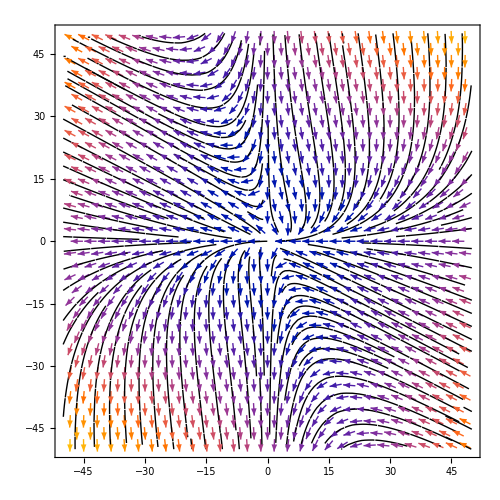

```mathematica
StreamPlot[{2x-x^2+x*y, 3y-2x*y-y^2}, {x, -50, 50}, {y, -50,
   50}, VectorPoints -> 30, StreamPoints -> Fine, 
 StreamColorFunction -> None,  StreamStyle -> {Black, "Segment"},
 AspectRatio -> Automatic, ImageSize -> 500]
```

```mathematica
D[(2x-x^2+x*y), x]/.x->0/.y->0
D[(2x-x^2+x*y), y]/.x->0/.y->0
D[(3y-2x*y-y^2), x]/.x->0/.y->0
D[(3y-2x*y-y^2), y]/.x->0/.y->0
```

2

0

0

3

```mathematica
J={{D[(2x-x^2+x*y), x]/.x->0/.y->0,D[(2x-x^2+x*y), y]/.x->0/.y->0},{D[(3y-2x*y-y^2), x]/.x->0/.y->0,D[(3y-2x*y-y^2), y]/.x->0/.y->0}}
```

{{2,0},{0,3}}